# Machine Learning I

## Wolfram Summer School 2019

```mathematica
-Graphics-       -Graphics-
```

## Machine Learning

### Machine Learning ?

Programming without giving explicit instruction

Typically, a computer “learns” a model from data

model = program with tunable parameters

learning = tuning parameters to fit data

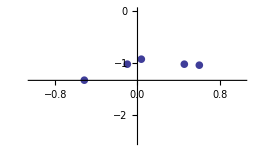
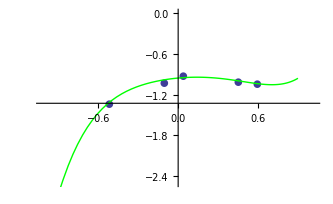
-Graphics-	⟶	-Graphics-

{ →cat, →dog,...}	⟶	-Graphics-

### Typical tasks

Classification of images, sound, text, etc.

→cat, →dog,...

Prediction of a variable in a dataset

(6 yo, female) → 1.15 m, (11 yo, male) → 1.48 m, ...

Text translation

“the house is blue” → “la maison est bleue”

Prediction of a time series

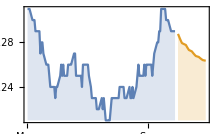

Anomaly detection

-Graphics-

Data clustering

-Graphics-

Robot learning how to walk

-Graphics-

## Learning Paradigm

### Supervised learning

Input → output mapping from examples

Most common paradigm

Wolfram Language functions:

Classify

Predict

### Unsupervised learning

Only outputs

On the rise

Wolfram Language functions:

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

SequencePredict

LearnDistribution

AnomalyDetection

SynthesizeMissingValues

### Reinforcement learning

Active agent, feedback from environment

Not much used yet (but lot of research)

Wolfram Language functions:

BayesianMinimization

ActiveClassification, ActivePrediction

Other tasks:

Learning policy

### Related field: Data mining

Wolfram Language functions:

FindFormula

FindDistribution

## Machine Learning in the Wolfram Language

### Automatic Machine Learning Framework

Functions:

Classify & Predict

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

...

Task oriented

Automatic

### Neural network framework

Model oriented

High flexibility

High performance

```mathematica
NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

NetGraph[<>]

### Functions developed using Machine Learning

Pre-trained network (NetModel)

Built-in classifiers

ImageIdentify, TextCases, etc.

## Built-in Machine Learning

### Pre-trained networks (NetModel)

```mathematica
NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
NetModel["LeNet TraiNened on MNIST Data"]
```

```mathematica
net=NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
Dynamic[Image/@NetTake[net,20][CurrentImage[]]]
```

```mathematica
ImageContents[-Graphics-]
```

Dataset[<>]

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
net[-Graphics-]
```

tee shirt

### Built-in Classifiers

```mathematica
lang=Classify["Language"]
```

ClassifierFunction[…]

```mathematica
lang["what is this?"]
```

English

```mathematica
DynamicModule[{x=""},
Column[{
InputField[Dynamic[x], String, ContinuousAction->True],Dynamic[Column@Classify["Language",x,"TopProbabilities"->3]]
}]]
```

```mathematica
DynamicModule[{x=""},
Column[{
InputField[Dynamic[x], String, ContinuousAction->True],Dynamic[Column@Classify["FacebookTopic",x,"TopProbabilities"->3]]
}]]
```

### ImageIdentify, ImageCases

```mathematica
im=CurrentImage[]
```

```mathematica
ImageContents[-Graphics-]
```

```mathematica
imageCaption[i_Image] := With[
	{detections = Length /@ ImageCases[i, AcceptanceThreshold -> .5]},
	If[Length[detections]==0,
		"An image with no identified objects.",
		StringJoin[
			"An image with ",
			Riffle[
				Riffle[
					KeyValueMap[
						StringRiffle[{IntegerName[#2], Pluralize[#1["Name"],#2]}]&,
						detections
					],
					", ",
					{2, -3, 2}
				], 
				" and ", 
				{-2, -2, 1}
			],
			"."
		]
	]
]
```

```mathematica
imageCaption[-Graphics-]
```

### AudioIdentify

```mathematica
AudioIdentify[]
```

Chirp, tweet

```mathematica
net=NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"]
```

NetChain[<>]

### TextStructure

```mathematica
TextStructure["This lecture is so cool!"]
```

```mathematica
{{{{" "{{" "{{"This"}, {"Determiner"}}{{"lecture"}, {"Noun"}}}, {"Noun Phrase"}}{{" "{{"is"}, {"Verb"}}{{" "{{"so"}, {"Adverb"}}{{"cool"}, {"Adjective"}}}, {"Adjective Phrase"}}}, {"Verb Phrase"}}{{"!"}, {"Punctuation"}}}, {"Sentence"}}}}//InputForm
```

### FindTextualAnswer

http://blog.wolfram.com/2018/02/15/new-in-the-wolfram-language-findtextualanswer/

```mathematica
FindTextualAnswer["The dodo (Raphus cucullatus) is an extinct flightless bird that was endemic to the island of Mauritius, east of Madagascar in the Indian Ocean. The dodo's closest genetic relative was the also extinct Rodrigues solitaire, the two forming the subfamily Raphinae of the family of pigeons and doves. The closest living relative of the dodo is the Nicobar pigeon. A white dodo was once thought to have existed on the nearby island of Réunion, but this is now thought to have been confusion based on the Réunion ibis and paintings of white dodos.\n
Subfossil remains show the dodo was about 1 metre (3 ft 3 in) tall and may have weighed 10.6–17.5 kg (23–39 lb) in the wild. The dodo's appearance in life is evidenced only by drawings, paintings, and written accounts from the 17th century.",
"How big was the dodo?"]
```

1 metre

```mathematica
NetModel["Wolfram FindTextualAnswer Net for WL 11.3"]
```

NetGraph[<>]

### TextCases

```mathematica
TextContents["The flag of Italy is green, white and red. Since 1861, the capital is Rome, which also serves as the capital of the Lazio region. With 2,872,800 residents in 1,285 km2 (496.1 sq mi)"]
```

```mathematica
DynamicModule[{x=""},Column[{InputField[Dynamic[x], String, ContinuousAction->True],Dynamic[TextContents[x]]}]]
```

```mathematica
TextCases[StringTake[WikipediaData["Planets"],10000],"Planet"]
```

```mathematica
TextCases[StringTake[WikipediaData["Planets"],10000],{"Person", "Planet"}]
```

```mathematica
TextCases[StringTake[WikipediaData["Planets"],10000],LinguisticAssistant->"HighlightedSnippet"]
```

```mathematica
NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

```mathematica
NetModel["Wolfram Entity Recognition Net for TextCases WL 12.0 V2"]
```

## Dataset of images

```mathematica
classes={"jellyfish","blackberry","octopus","blueberry"};
```

```mathematica
images=WebImageSearch[#,"Thumbnails",MaxItems->30] & /@classes;
```

```mathematica
flatimages =RandomSample[Flatten[images]];
```

```mathematica
flatimages
```

## FeatureSpacePlot

```mathematica
FeatureSpacePlot[flatimages]
```

-Graphics-

## Search system

```mathematica
Length[flatimages]
```

40

```mathematica
dataset=flatimages[[;;90]];
queries = flatimages[[91;;]];
```

```mathematica
nf=FeatureNearest[dataset]
```

## Classify & Predict - simple examples

### Classify

```mathematica
c=Classify[{1->"A",2->"A",3->"B",4->"B"}]
```

ClassifierFunction[…]

```mathematica
c[1.5]
```

A

```mathematica
c[1.5,"Probabilities"]
```

<|A→0.833333,B→0.166667|>

### Predict

```mathematica
p=Predict[{1->1.3,2->4.3,4->5.5,8.6->2.3}]
```

PredictorFunction[…]

```mathematica
p[1.5]
```

3.35

```mathematica
p[1.5,"Distribution"]
```

NormalDistribution[3.35,1.64545]

## Image Classification

```mathematica
dataset=Thread/@Thread[images->classes];
```

```mathematica
dataset =RandomSample[Flatten[dataset]];
```

```mathematica
dataset
```

```mathematica
Length[dataset]
```

120

```mathematica
trainingset=dataset[[;;80]];
testset=dataset[[81;;]];
```

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
testset[[1]]
```

-Graphics-→blueberry

```mathematica
c[-Graphics-]
```

blueberry

```mathematica
c[-Graphics-,"Probabilities"]
```

<|blackberry→7.65348×10^-13,blueberry→1.,jellyfish→3.6985×10^-25,octopus→6.07961×10^-25|>

```mathematica
cm=ClassifierMeasurements[c,testset]
```

ClassifierMeasurementsObject[…]

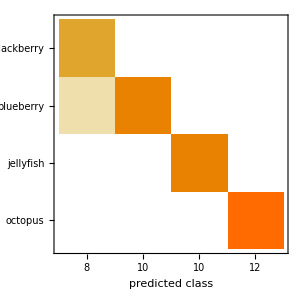
Classifier Measurements
Number of test examples | 40
Accuracy | (97.52.5) %
Accuracy baseline | (30.7.) %
Geometric mean of probabilities | 0.837 ± 0.15
Mean cross entropy | 0.178 ± 0.18
Single evaluation time | 132. ms/example
Batch evaluation speed | 8.77 examples/s
Rejection rate | 0 %
-Graphics- |

```mathematica
cm["Report"]
```

```mathematica
cm["Examples"->{"blueberry","blackberry"}]
```

{-Graphics-→blueberry}

```mathematica
cm["Examples"->{"blackberry","blackberry"}]
```

```mathematica
cm["BestClassifiedExamples"]
```

{-Graphics-→blueberry,-Graphics-→blackberry,-Graphics-→jellyfish,-Graphics-→octopus,-Graphics-→blackberry,-Graphics-→blueberry,-Graphics-→octopus,-Graphics-→jellyfish,-Graphics-→blackberry,-Graphics-→jellyfish}

```mathematica
c[-Graphics-,"Probabilities"]
```

<|blackberry→6.72937×10^-20,blueberry→1.5931×10^-12,jellyfish→0.0313702,octopus→0.96863|>

```mathematica
cm["WorstClassifiedExamples"]
```

{-Graphics-→blueberry,-Graphics-→octopus,-Graphics-→octopus,-Graphics-→octopus,-Graphics-→octopus,-Graphics-→jellyfish,-Graphics-→jellyfish,-Graphics-→octopus,-Graphics-→blueberry,-Graphics-→jellyfish}

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

```mathematica
CurrentImage[]
```

```mathematica
c[-Graphics-,"Probabilities"]
```

<|blackberry→0.504043,blueberry→6.22247×10^-7,jellyfish→0.495956,octopus→1.3112×10^-10|>

## Text classification

```mathematica
topics=Get["~/Presentations/SS2017/topic.m"];
```

```mathematica
topics
```

```mathematica
Length@topics
```

470000

```mathematica
RandomSample[topics,5]
```

```mathematica
topicclassifier=Classify[topics[[;;100000]]]
```

ClassifierFunction[…]

```mathematica
Information[topicclassifier]
```

Classifier information
Data type | Text
Number of classes | 26
Accuracy | (55.50.5) %
Method | Markov
Single evaluation time | 3.45 ms/example
Batch evaluation speed | 1.47 examples/ms
Loss | 2.89 ± 0.045
Model memory | 17.4 MB
Training examples used | 100000 examples
Training time | 47. s
 |

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@topicclassifier[text,"TopProbabilities"->3]]
```

## Data Prediction

http://datarepository.wolframcloud.com/

```mathematica
ResourceSearch["Boston"]
```

Dataset[<>]

```mathematica
object=First@ResourceSearch["Boston"]
```

Dataset[<>]

```mathematica
dataset=ResourceData["Sample Data: Boston Homes"]
```

Dataset[<>]

```mathematica
trainingset=dataset[[;;400]];
testset=dataset[[400;;]];
```

```mathematica
p=Predict[trainingset->"MEDV",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,testset->"MEDV"]
```

PredictorMeasurementsObject[…]

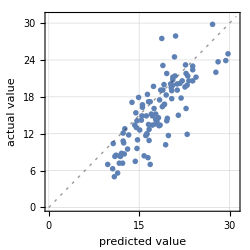
Predictor Measurements
Number of test examples | 107
Standard deviation | 3.93 ± 0.27
Standard deviation baseline | 5.37 ± 0.31
Mean cross entropy | 2.79 ± 0.071
Single evaluation time | 12.9 ms/example
Batch evaluation speed | 1.36 examples/ms
-Graphics- |

```mathematica
pm["Report"]
```

## Good practices

Shuffle the dataset (RandomSample)

Separate training set from test set

Start with a small training set

Just need a laptop in the beginning

Start using simple functions

e.g. Classify or Predict on raw data for a baseline

Plot a learning curve (performance vs. training set size)